## Дополнительные функции:

```mathematica
MakeTable[{points_,fValues_,norms_}]:=Module[{gridLabel,gridData,i},
gridLabel={"k","(X^k)","f(X^k)","r"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,Length[points]}];
(*в 1-м столбце-номер итерации*)
gridData[[All,1]]=Table[i,{i,0,Length[points]-1}];
(*во 2-м столбце-точки траектории*)
For[i=1,i≤Length[points],i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],4]]<>", "<>ToString[SetAccuracy[points[[i,2]],4]]<>" )"];
(*в 3-м столбце-значение функции*)
gridData[[All,3]]=SetAccuracy[fValues,4];
(*в 4-м столбце-значение нормы невязки*)
gridData[[All,4]]=SetAccuracy[norms,4];
gridData={gridLabel}~Join~gridData;
(*выводим всю таблицу*)
Grid[gridData,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
];
PlotMethod[func_,limit_,setX_,setY_,{points_,fValues_}]:=Module[{},
Show[ContourPlot[func[{x,y}],setX,setY,Contours->fValues,ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{func[{x,y}]}]],FrameStyle->Thick,ImageSize->350,PlotPoints->100,Epilog->{Purple,Thickness[0.001],Arrowheads[.02],Table[Arrow[points[[i-1;;i]]],{i,2,Length[points]}],Darker[Red],PointSize[0.015],Point[points[[1;;-1]]],Yellow,Point[points[[-1]]]}],ContourPlot[limit[{x,y}]==0,setX,setY,ContourStyle->Black],ContourPlot[limit[{x,y}]==-0.05,setX,setY,ContourStyle->Red]]
];
PlotNorms[norms_]:=Module[{},
ListLogPlot[norms,PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k","||w^k||"},ImageSize->700,Joined->True,Mesh->Full, MeshStyle->Directive[PointSize[0.02],Red]]
];
Antigrad[point_, func_] := -Grad[func[{x, y}], {x, y}] /. {x->point[[1]],y->point[[2]]};
Hesse[ func_] := D[func[{x,y}],{{x,y},2}] ;
CalcHesse[MHesse_,{xp_,yp_}]:=MHesse/.{x -> xp, y -> yp};
MakePositive[Hesse_,k_]:=Module[{H = Hesse,n = Length@Hesse},
If[PositiveDefiniteMatrixQ[Hesse],
Return[H],
H = MakePositive[H+k*IdentityMatrix[n],k];
];
Return[H]
];
```

## Алгоритм

```mathematica
Newton[{x0_, y0_},func_,ϵ_,split_,w_,ν_] :=Module [
{points = {{x0, y0}},funcpoints = {},ω = {},norms = {},H = Hesse[func],CalcH,InvH,CalcInvH,Positive,κ={1}},
Positive = PositiveDefiniteMatrixQ[H];
InvH = Inverse[H];
funcpoints ={ func[Last@points] };
ω = {Antigrad[Last@points, func]};
norms = {Norm[Last@ω]};
While[Last@norms ≥ ϵ,
If[Not@Positive,
CalcH = MakePositive[CalcHesse[H,Last@points],10];
CalcInvH = Inverse[CalcH],
CalcInvH = CalcHesse[InvH,Last@points];
];
AppendTo[points, Last@points +Last@κ* CalcInvH .Last@ω//N];
AppendTo[funcpoints, func[Last@points]];
If[split,
If[funcpoints[[-1]]-funcpoints[[-2]]≥ -w*Last@κ*(Last@ω.(CalcInvH.Last@ω)),
AppendTo[κ,Last@κ],
AppendTo[κ,Last@κ*ν];
];
];

AppendTo[ω, Antigrad[Last@points, func] ];
AppendTo[norms, Norm[Last@ω]];

];
{points[[-1]], funcpoints[[-1]]}
];
```

```mathematica
Algorithm[point_,f_,g_,ϵ_,Cond_] := Module [{points={0,point},values={0,f[point]},r={1},result},
While[Abs[values⟦-1⟧-values⟦-2⟧]≥ϵ&&g[points⟦-1⟧]<= 0,
If[Cond==True,
result = FindMinimum[f[{x,y}]-r⟦-1⟧/g[{x,y}]-r⟦-1⟧/(g[{x,y}])^2,{{x,points⟦-1,1⟧},{y,points⟦-1,2⟧}}],
result = FindMinimum[f[{x,y}]-r⟦-1⟧/g[{x,y}],{{x,points⟦-1,1⟧},{y,points⟦-1,2⟧}}];
];
AppendTo[points,{result[[2,1,2]],result[[2,2,2]]}];
AppendTo[values,result⟦1⟧];
AppendTo[r,r⟦-1⟧/2];
];
{points,values,r}
];
```

## Функции:

```mathematica
(*3/4 x^2+5/4 x-2-y;*)
```

```mathematica
g[{x_,y_}]:=3/4 x^2+5/4 x-2-y;
rosenbrok[{x_,y_}]:=(1-x)^2+(y-x^2)^2;
```

## Вычисления:

```mathematica
ϵ=10^-3;
```

### Первый пример:

```mathematica
func =rosenbrok;(*x0 = {-1,-2}*)
Res = Algorithm[{-1,-2},func,g,ϵ,False];
X= Res[[1,2;;]];
val= Res[[2,2;;]];
r = Res[[3]];
setX = {x,-4,4};
setY ={y,-4,4};
```

### Второй пример:

```mathematica
Length[#]&/@{X,val,r}
```

{12,12,12}

## Результаты:

```mathematica
MakeTable[{X,val,r}]
```

k | (X^k) | f(X^k) | r
0 | ( -1.000, -2.000 ) | 13. | 1.
1 | ( 0.787, 0.868 ) | 0.812 | 0.5
2 | ( 0.871, 0.917 ) | 0.439 | 0.25
3 | ( 0.926, 0.951 ) | 0.232 | 0.125
4 | ( 0.959, 0.973 ) | 0.12 | 0.063
5 | ( 0.978, 0.986 ) | 0.061 | 0.031
6 | ( 0.989, 0.992 ) | 0.031 | 0.016
7 | ( 0.994, 0.996 ) | 0.016 | 0.008
8 | ( 0.997, 0.998 ) | 0.008 | 0.004
9 | ( 0.999, 0.999 ) | 0.004 | 0.002
10 | ( 0.999, 1.00 ) | 0.002 | 0.001
11 | ( 1.00, 1.00 ) | 0.001 | 0.0005

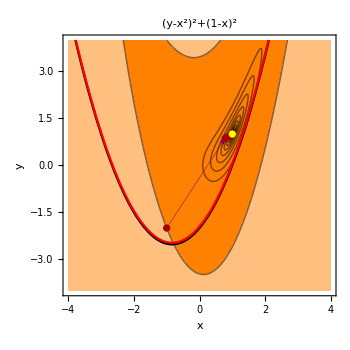

```mathematica
PlotMethod[func,g,setX,setY,{X,val}]
```

```mathematica
Manipulate[Plot3D[func[{x,y}]-r/g[{x,y}],setX,setY,AxesLabel->{"x","y","z"}],{r,10^-5,1000}]
```